```mathematica
Clear[p,qr,qw,a]
(*Define the rate matrix*)
M={{-2*p*a,p*a,p*a,0,0},
{qr*a,-(qr*a+p*a),0,p*a,0},
{qw*a,0,-(qw*a+p),0,p},
{0,qr*a,0,-(qr*a+w),0},
{0,0,qr,0,-(qr+w)}};
(*Define source terms for right and wrong pathways*)
NR={0,0,0,w,0};
NW={0,0,0,0,w};
(*Solve for Laplace transformed *)
s=0;
FR=LinearSolve[s*IdentityMatrix[5]-M,-NR];
FW=LinearSolve[s*IdentityMatrix[5]-M,-NW];

(*Splitting probabilities*)
PiR=FR[[1]];  (*From initial state to R*)
PiW=FW[[1]];  (*From initial state to W*)

(*Compute derivative for MFPT:solve (M-sI) dFds=F(s)*)
dFRds=LinearSolve[M,FR];  (*At s=0*)
dFWds=LinearSolve[M,FW];  (*At s=0*)

(*Conditional MFPT to reach R*)
tauR=-(1/PiR)*dFRds[[1]];

(*Conditional MFPT to reach W*)
tauW=-(1/PiW)*dFWds[[1]];

(*Display results*)
Print["Splitting probability to R: ",PiR];
Print["Splitting probability to W: ",PiW];
Print["Conditional MFPT to R: ",tauR];
Print["Conditional MFPT to W: ",tauW];
```

Splitting probability to R: (-a qr qw-p w-a qw w)/(a qr^2+a qr qw+2 p w+qr w+a qw w)

Splitting probability to W: (-a qr^2-p w-qr w)/(a qr^2+a qr qw+2 p w+qr w+a qw w)

Conditional MFPT to R: -((a^3 p^2 qr^3 qw+a^3 p qr^4 qw+a^3 p^2 qr^2 qw^2+a^3 p qr^3 qw^2+a^3 qr^4 qw^2+4 a^2 p^3 qr qw w+6 a^2 p^2 qr^2 qw w+3 a^2 p qr^3 qw w+2 a^3 p qr^3 qw w+2 a^3 p^2 qr qw^2 w+2 a^2 p qr^2 qw^2 w+2 a^3 p qr^2 qw^2 w+a^2 qr^3 qw^2 w+2 a^3 qr^3 qw^2 w+2 a p^4 w^2+3 a p^3 qr w^2+a p^2 qr^2 w^2+3 a^2 p^3 qw w^2+5 a p^2 qr qw w^2+6 a^2 p^2 qr qw w^2+2 a p qr^2 qw w^2+4 a^2 p qr^2 qw w^2+a^3 p qr^2 qw w^2+a^3 p^2 qw^2 w^2+4 a^2 p qr qw^2 w^2+a^3 p qr qw^2 w^2+2 a^2 qr^2 qw^2 w^2+a^3 qr^2 qw^2 w^2+3 p^3 w^3+p^2 qr w^3+5 a p^2 qw w^3+a^2 p^2 qw w^3+2 a p qr qw w^3+a^2 p qr qw w^3+2 a^2 p qw^2 w^3+a^2 qr qw^2 w^3)/(a p^2 w (-a qr qw-p w-a qw w) (a qr^2+a qr qw+2 p w+qr w+a qw w)))

Conditional MFPT to W: -((a^3 p^2 qr^4+a^3 p qr^5+a^3 p^2 qr^3 qw+a^3 p qr^4 qw+a^3 qr^5 qw+4 a^2 p^3 qr^2 w+6 a^2 p^2 qr^3 w+3 a^2 p qr^4 w+a^3 p qr^4 w+2 a^3 p^2 qr^2 qw w+4 a^2 p qr^3 qw w+a^3 p qr^3 qw w+2 a^2 qr^4 qw w+a^3 qr^4 qw w+2 a p^4 w^2+5 a p^3 qr w^2+8 a p^2 qr^2 w^2+3 a^2 p^2 qr^2 w^2+3 a p qr^3 w^2+2 a^2 p qr^3 w^2+a^2 p^3 qw w^2+a p^2 qr qw w^2+a^2 p^2 qr qw w^2+3 a p qr^2 qw w^2+4 a^2 p qr^2 qw w^2+a qr^3 qw w^2+2 a^2 qr^3 qw w^2+p^3 w^3+2 a p^3 w^3+3 p^2 qr w^3+3 a p^2 qr w^3+p qr^2 w^3+a p qr^2 w^3+a p^2 qw w^3+3 a p qr qw w^3+a qr^2 qw w^3)/(a p^2 w (-a qr^2-p w-qr w) (a qr^2+a qr qw+2 p w+qr w+a qw w)))

```mathematica
ProbRatio=PiR/PiW;
Simplifiedratio=FullSimplify[ProbRatio];
Print["Accuracy Ratio:",Simplifiedratio];
```

Accuracy Ratio:(p w+a qw (qr+w))/(a qr^2+(p+qr) w)

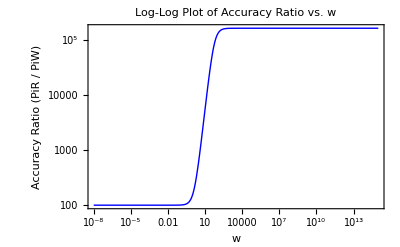

```mathematica
(*Define Parameters*)
p=2;
qr=1;
qw=100;
a=5000;  (* For thermodynamic 1/ For kinetic 5000*)

(*Define Conditional MFPT function to R*)
ConditionalMFPTtoR[w_]:=-((a^3*p^2*qr^3*qw+a^3*p*qr^4*qw+a^3*p^2*qr^2*qw^2+a^3*p*qr^3*qw^2+a^3*qr^4*qw^2+4*a^2*p^3*qr*qw*w+6*a^2*p^2*qr^2*qw*w+3*a^2*p*qr^3*qw*w+2*a^3*p*qr^3*qw*w+2*a^3*p^2*qr*qw^2*w+2*a^2*p*qr^2*qw^2*w+2*a^3*p*qr^2*qw^2*w+a^2*qr^3*qw^2*w+2*a^3*qr^3*qw^2*w+2*a*p^4*w^2+3*a*p^3*qr*w^2+a*p^2*qr^2*w^2+3*a^2*p^3*qw*w^2+5*a*p^2*qr*qw*w^2+6*a^2*p^2*qr*qw*w^2+2*a*p*qr^2*qw*w^2+4*a^2*p*qr^2*qw*w^2+a^3*p*qr^2*qw*w^2+a^3*p^2*qw^2*w^2+4*a^2*p*qr*qw^2*w^2+a^3*p*qr*qw^2*w^2+2*a^2*qr^2*qw^2*w^2+a^3*qr^2*qw^2*w^2+3*p^3*w^3+p^2*qr*w^3+5*a*p^2*qw*w^3+a^2*p^2*qw*w^3+2*a*p*qr*qw*w^3+a^2*p*qr*qw*w^3+2*a^2*p*qw^2*w^3+a^2*qr*qw^2*w^3)/(a*p^2*w*(-a*qr*qw-p*w-a*qw*w)*(a*qr^2+a*qr*qw+2*p*w+qr*w+a*qw*w)));

(*Define v as a function of w*)
v[w_]:=w/ConditionalMFPTtoR[w];

(*Define Accuracy Ratio as a function of v*)
AccuracyRatio[v_]:=(p*v+a*qw*(qr+v))/(a*qr^2+(p+qr)*v);

(*Plot Accuracy Ratio as a function of w*)LogLogPlot[AccuracyRatio[v[w]],{w,10^-8,10^15},PlotRange->All,AxesLabel->{"w","Accuracy Ratio (PiR / PiW)"},PlotLabel->"Log-Log Plot of Accuracy Ratio vs. w",PlotStyle->{Blue,Thick},Frame->True]
```